```mathematica
c=1
L0=1
T0=L0/c

gam0=2
rhor0=1
b0=10
r0=L0

vroc=0.9
(*vroc=0*)
eta[r_]:=If[r≥r0,0,Evaluate[vroc*L0^2/T0]]
vr=0.1*vroc*c
rho0[r_]:=rhor0/((r/r0)^2*(gam[r]/gam0))
Delta0[r]:=8*Pi*L0
QEM[r_]:=2*(b[r]^2/(4*Pi))*vr/Delta0[r]
QEM[r_]:=0
esq[r_]:=eta[r]^2/(c^4*r^2)*(-c/(4*Pi)*D[r*b[r]*gam[r],r])^2
eq1=(1/r^2)*D[r^2*(rho0[r]+(esq[r]+b[r]^2)/(4*Pi))*gam[r]^2*c^2,r]==0
(*eq1=(1/r^2)*D[r^2*(rho0[r]+b[r]^2/(4*Pi))*gam[r]^2*c^2,r]==-QEM[r]*gam[r]*c*)
(*eq2=D[c*r*b[r]*gam[r]-c*eta[r]/(4*Pi*gam[r])*D[r*b[r]*gam[r],r],r]==0*)
eq2=D[c*r*b[r]*gam[r]-c*eta[r]/(4*Pi*gam[r])*D[r*b[r]*gam[r],r],r]==0
```

1

1

1

2

1

10

1

0.9

0.09

1/r^2(2 r gam[r]^2 (2/(r^2 gam[r])+(b[r]^2+(If[r≥1,0,0.9]^2 (b[r] gam[r]+r gam[r] b'[r]+r b[r] gam'[r])^2)/(16 π^2 r^2))/(4 π))+2 r^2 gam[r] gam'[r] (2/(r^2 gam[r])+(b[r]^2+(If[r≥1,0,0.9]^2 (b[r] gam[r]+r gam[r] b'[r]+r b[r] gam'[r])^2)/(16 π^2 r^2))/(4 π))+r^2 gam[r]^2 (-4/(r^3 gam[r])-(2 gam'[r])/(r^2 gam[r]^2)+1/(4 π)(2 b[r] b'[r]+(If[r≥1,0,0] If[r≥1,0,0.9] (b[r] gam[r]+r gam[r] b'[r]+r b[r] gam'[r])^2)/(8 π^2 r^2)-(If[r≥1,0,0.9]^2 (b[r] gam[r]+r gam[r] b'[r]+r b[r] gam'[r])^2)/(8 π^2 r^3)+1/(8 π^2 r^2)If[r≥1,0,0.9]^2 (b[r] gam[r]+r gam[r] b'[r]+r b[r] gam'[r]) (2 gam[r] b'[r]+2 b[r] gam'[r]+2 r b'[r] gam'[r]+r gam[r] b''[r]+r b[r] gam''[r]))))==0

b[r] gam[r]+r gam[r] b'[r]+r b[r] gam'[r]-(If[r≥1,0,0] (b[r] gam[r]+r gam[r] b'[r]+r b[r] gam'[r]))/(4 π gam[r])+(If[r≥1,0,0.9] gam'[r] (b[r] gam[r]+r gam[r] b'[r]+r b[r] gam'[r]))/(4 π gam[r]^2)-(If[r≥1,0,0.9] (2 gam[r] b'[r]+2 b[r] gam'[r]+2 r b'[r] gam'[r]+r gam[r] b''[r]+r b[r] gam''[r]))/(4 π gam[r])==0

```mathematica
q[r_]:=b0/(r/r0)
gat[r_]:=gam0
FullSimplify[eq1//.{b->q,gam->gat}]
FullSimplify[eq2//.{b->q,gam->gat}]
```

True

True

```mathematica
s=NDSolve[{eq1,eq2,gam[1]==2,b[1]==10,gam'[1]==0,b'[1]==-10},{b[r],gam[r]},{r,1,10},MaxSteps->100000]
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

{{b[r]→InterpolatingFunction[{{1.,10.}},<>][r],gam[r]→InterpolatingFunction[{{1.,10.}},<>][r]}}

```mathematica
b[r]/.s//.{r->1.3}
```

{7.69231}

InterpolatingFunction::dmval: Input value {0.00004703852404259265`} lies outside the range of data in the interpolating function. Extrapolation will be used.

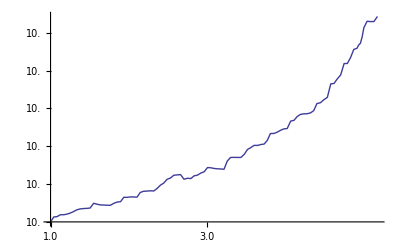

InterpolatingFunction::dmval: Input value {0.00004703852404259265`} lies outside the range of data in the interpolating function. Extrapolation will be used.

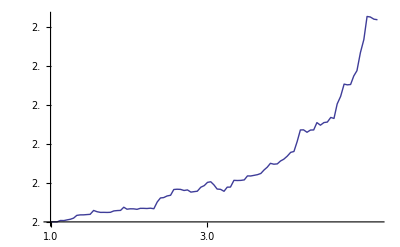

```mathematica
LogLogPlot[r*Evaluate[b[r]/.s],{r,1,10},PlotRange->All]
LogLogPlot[Evaluate[gam[r]/.s],{r,1,10},PlotRange->All]
```

```mathematica
DSolve[{eq1,b[r0]==b0},{b[r]},r]
```

DSolve::bvnr: For some branches of the general solution, the given boundary conditions do not restrict the existing freedom in the general solution.

{{b[r]→0},{b[r]→(b0 ⅇ^(-(r vr)/(c gam0 L0)+(r0 vr)/(c gam0 L0)) r0)/r}}

```mathematica
q[r_]:=(b0 ⅇ^(-(r vr)/(c gam0 L0)+(r0 vr)/(c gam0 L0)) r0)/r
god=FullSimplify[eq2//.{b->q}]
god//.{vr->0}
```

(b0 ⅇ^(((-r+r0) vr)/(c gam0 L0)) r0 (4 c gam0^2 L0 π+eta vr))/(gam0 L0)==4 C2 π

4 b0 c gam0 π r0==4 C2 π